```mathematica
f[x,y,z][[2]]
```

y

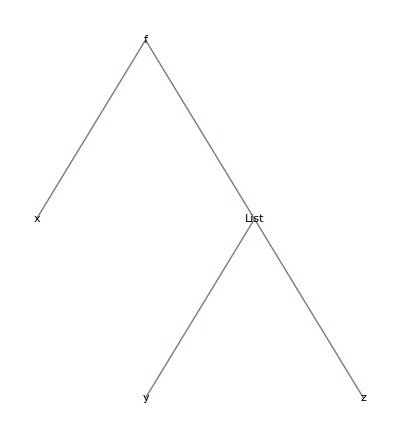

```mathematica
TreeForm[f[x,{y,z}]]
```

```mathematica
f[x,y,z]
```

f[x,y,z]

```mathematica
Head[%]
```

f

```mathematica
Head[{1,2,3}]
```

List

```mathematica
Head[2/3]
```

Rational

```mathematica
x
```

x

```mathematica
Head[x]
```

Symbol

```mathematica
x[[1]]
```

Part::partd: Part specification x⟦1⟧ is longer than depth of object.

x⟦1⟧

```mathematica
Depth[x]
```

1

```mathematica
Head[x]
```

Symbol

```mathematica
Head[x_->1]
```

Rule

```mathematica
Head[(x_->1)]
```

Rule

```mathematica
Head[Head]
```

Symbol

```mathematica
Head
```

Head

```mathematica
FullForm[#^2&]
```

Function[Power[Slot[1],2]]

```mathematica
f = Function[Slot[1]+Slot[2]]
```

#1+#2&

```mathematica
Delayed[f[1,2]]
```

Delayed[f[1,2]]

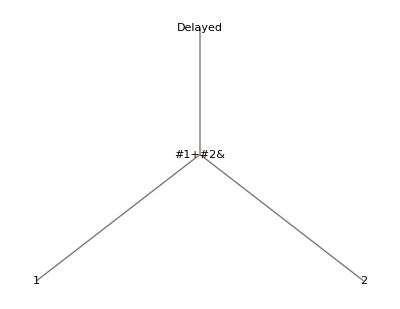

```mathematica
TreeForm[%]
```

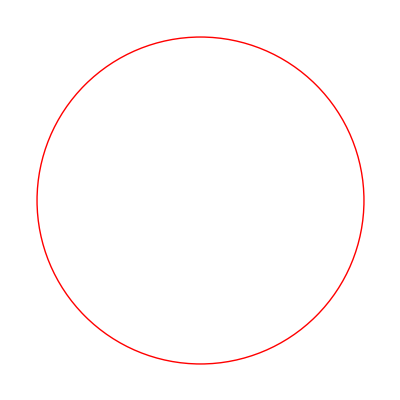

```mathematica
Graphics[Style[Circle[{0,0},10],Red]]
```

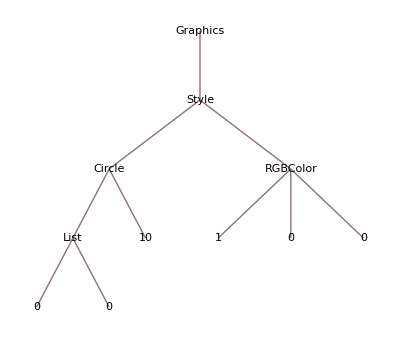

```mathematica
TreeForm[%]
```

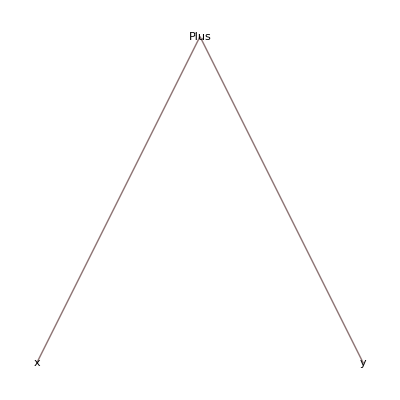

```mathematica
TreeForm[x+y]
```

```mathematica
3^100
```

515377520732011331036461129765621272702107522001

```mathematica
IntegerDigits[3^100]//Counts//KeySort//Values
```

{7,9,9,5,1,5,4,7,1}

```mathematica
34.2
```

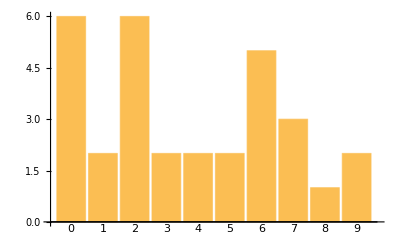

```mathematica
IntegerDigits[2^100]//Counts//KeySort//BarChart[#,ChartLabels->Automatic]&
```

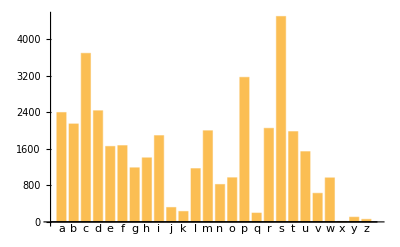

```mathematica
First/@Characters/@WordList[]//ToLowerCase//Counts//KeySort//BarChart[#,ChartLabels->Automatic]&
```

```mathematica
(x = First/@Characters/@WordList[]//ToLowerCase//Counts//Sort)[[-5;;]]
```

<|a→2397,d→2436,p→3168,c→3694,s→4502|>

```mathematica
(First/@Characters/@(If[MemberQ[Alphabet["English"],#],#," "]&/@(WikipediaData["Computers"]//ToLowerCase//Characters)//StringJoin//StringSplit)//Counts//Sort)[[-5;;]]
```

<|o→645,i→690,c→823,a→1080,t→1310|>

```mathematica
If[MemberQ[#,Alphabet["English"]],#," "]&/@Alphabet["English"]
```

{ , , , , , , , , , , , , , , , , , , , , , , , , , }

```mathematica
Alphabet["English"]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
MemberQ[
```

```mathematica
#q/#u&@(WikipediaData["Computers"]//ToLowerCase//Characters//Counts)//N
```

0.0400509

```mathematica
((If[MemberQ[Alphabet["English"],#],#," "]&/@(ExampleData[{"Text","AliceInWonderland"}]//ToLowerCase//Characters))//StringJoin//StringSplit//Counts//Sort)[[-20;;]]
```

<|had→65,s→66,with→67,at→79,as→91,that→105,her→108,you→118,said→144,in→163,alice→167,was→167,i→178,it→189,of→199,she→242,to→252,a→278,and→338,the→632|>

```mathematica
rules = Rule @@@((Partition[#,2,1]&/@ Characters/@WordList[Language->"Russian"])//Flatten[#,1]&)
```

{а→г,г→а,а→д,д→а,а→р,р→ф,б→а,а→р,б→а,а→с,б→е,е→г,б→е,е→з,б→е,е→й,б→и,и→л,б→и,и→т,б→о,о→г,б→о,о→й,б→о,о→к,б→о,о→р,б→о,о→ю,б→о,о→я,б→у,у→к,б→ы,ы→к,б→ы,ы→л,225864,с→о,о→в,в→о,о→с,с→с,с→т,т→а,а→н,н→о,о→в,в→и,и→т,т→е,е→л,л→ь,ь→н,н→ы,ы→х,п→р,р→е,е→д,д→в,в→о,о→д,д→и,и→т,т→е,е→л,л→ь,ь→с,с→т,т→в,в→у,у→е,е→м,м→ы,ы→м,м→и}
 |  |  |  |

```mathematica
rulecounts = rules//Counts
```

<|(а→г)→323,(г→а)→534,(а→д)→825,(д→а)→1001,(а→р)→724,(р→ф)→11,(б→а)→281,(а→с)→1577,(б→е)→809,(е→г)→520,(е→з)→529,(е→й)→581,(б→и)→424,(и→л)→1853,(и→т)→1731,(б→о)→596,(о→г)→1154,(о→й)→995,(о→к)→851,(о→р)→1499,(о→ю)→53,(о→я)→215,(б→у)→202,(у→к)→214,(б→ы)→231,(ы→к)→96,(ы→л)→229,(в→а)→2469,(а→л)→2942,(а→м)→916,(а→ш)→201,(в→е)→1803,(е→к)→324,(е→л)→1854,(е→с)→1511,(в→и)→1033,(и→д)→350,(в→н)→273,(н→е)→1854,(в→о)→1607,(о→д)→1727,(о→н)→875,(о→т)→1679,(в→с)→311,(с→е)→612,(с→ю)→9,(с→я)→2201,(в→ы)→1112,(в→я)→170,(я→з)→121,(г→д)→11,(д→е)→1283,(г→е)→62,(г→о)→1572,(о→л)→1596,(г→у)→193,(у→б)→303,(у→л)→583,(а→в)→1345,(а→н)→1615,(а→ю)→732,(д→в)→245,(е→д)→1080,(д→л)→142,(л→я)→637,(д→н)→487,(н→а)→2274,(н→и)→2293,(н→о)→2490,(н→у)→1146,(н→ю)→71,(н→я)→456,(д→о)→1125,(о→м)→1482,(д→у)→463,(у→х)→140,(д→ы)→274,(ы→м)→962,(л→е)→1735,(л→и)→2954,(л→о)→1851,(е→м)→1087,(м→у)→428,(с→т)→3733,(е→ш)→382,(ш→ь)→175,(е→щ)→136,(щ→е)→605,(ж→а)→636,(ж→д)→324,(д→и)→810,(ж→е)→705,(е→н)→2913,(ж→и)→642,(и→в)→1409,(ж→у)→115,(у→я)→30,(з→а)→1719,(з→л)→190,(л→а)→1947,(л→у)→544,(з→о)→332,(о→в)→2023,(з→р)→206,(р→я)→432,(з→у)→151,(у→д)→475,(и→б)→174,(и→г)→270,(г→л)→458,(и→з)→601,(и→м)→938,(м→и)→1414,(м→я)→85,(и→щ)→122,(щ→а)→314,(щ→и)→744,(щ→у)→132,(к→а)→1569,(а→к)→503,(к→е)→156,(к→о)→1668,(о→е)→622,(к→т)→42,(т→о)→1340,(к→у)→503,(у→ш)→297,(а→й)→255,(л→б)→12,(л→г)→37,(е→т)→1748,(л→ж)→46,(и→р)→335,(и→ц)→147,(о→б)→1393,(у→г)→244,(у→ж)→421,(у→н)→161,(у→ч)→301,(м→а)→670,(а→е)→615,(а→я)→982,(м→е)→983,(е→ж)→352,(е→ч)→394,(м→н)→284,(м→о)→648,(о→и)→196,(о→х)→325,(м→х)→3,(х→а)→159,(м→э)→4,(э→р)→8,(е→е)→314,(е→ю)→53,(и→х)→450,(и→ш)→136,(о→ж)→693,(о→с)→2468,(ю→х)→19,(п→а)→708,(а→х)→472,(п→е)→770,(п→и)→382,(и→к)→618,(п→н)→64,(п→о)→3339,(п→р)→2889,(р→и)→1503,(р→о)→2706,(п→с)→3,(с→а)→350,(с→ы)→152,(п→у)→392,(у→т)→696,(п→ь)→23,(ь→ю)→150,(р→а)→3267,(а→з)→1075,(р→в)→124,(р→е)→2322,(е→в)→780,(о→з)→506,(р→т)→173,(т→а)→1413,(т→у)→431,(т→ы)→576,(р→у)→777,(р→ы)→621,(я→д)→156,(е→р)→2034,(с→и)→431,(с→н)→426,(н→ы)→2262,(с→о)→909,(с→п)→790,(с→у)→262,(у→й)→37,(у→п)→377,(ы→н)→76,(ы→р)→149,(с→э)→1,(т→е)→1870,(е→х)→108,(т→и)→1070,(и→п)→98,(о→п)→651,(т→р)→1128,(т→ю)→15,(ю→к)→13,(у→в)→294,(у→з)→109,(з→ы)→197,(у→м)→331,(у→р)→217,(у→с)→710,(х→о)→613,(х→у)→43,(ч→и)→680,(ш→и)→1010,(у→ю)→558,(ю→т)→330,(ф→у)→14,(ч→а)→624,(ч→е)→636,(ч→т)→51,(ч→ь)→71,(ь→е)→153,(ь→и)→21,(ь→я)→111,(ш→а)→390,(ш→е)→746,(е→и)→69,(е→я)→98,(ш→л)→132,(л→ю)→265,(ш→о)→28,(ш→у)→118,(э→л)→6,(л→ь)→978,(э→т)→23,(э→х)→3,(ю→г)→5,(г→и)→230,(я→м)→263,(м→ы)→264,(я→р)→43,(р→д)→88,(а→т)→1610,(к→р)→870,(л→ы)→299,(ы→е)→629,(ы→й)→614,(р→к)→132,(к→и)→760,(ф→а)→29,(ф→ы)→15,(т→в)→877,(т→ь)→1860,(с→с)→265,(б→р)→623,(р→ю)→49,(д→ь)→50,(к→в)→27,(ы→т)→312,(б→ь)→28,(в→в)→11,(д→я)→198,(р→х)→37,(р→ь)→102,(с→ь)→1710,(щ→ь)→5,(в→з)→150,(з→я)→34,(я→в)→146,(я→л)→357,(я→т)→561,(и→ж)→133,(з→г)→164,(и→н)→948,(в→к)→71,(й→н)→132,(л→к)→148,(н→ь)→168,(с→к)→993,(ю→я)→1,(в→п)→46,(в→р)→172,(в→х)→17,(ы→ш)→169,(з→е)→135,(р→б)→17,(г→н)→262,(н→г)→10,(р→н)→374,(г→р)→436,(е→б)→222,(у→щ)→263,(а→ж)→400,(в→у)→238,(и→с)→1545,(и→ч)→282,(я→х)→137,(о→ч)→420,(д→р)→317,(у→е)→106,(х→е)→7,(х→и)→98,(ы→б)→87,(д→ю)→19,(ю→й)→4,(й→м)→29,(з→д)→327,(с→л)→824,(а→б)→374,(ж→г)→20,(ж→ж)→22,(я→ц)→10,(з→в)→438,(з→и)→190,(и→я)→505,(ы→х)→588,(з→м)→154,(з→н)→470,(д→т)→8,(и→ю)→118,(ю→л)→10,(ю→н)→24,(к→л)→358,(ю→в)→3,(ю→ч)→56,(к→н)→138,(р→м)→94,(о→ш)→271,(ы→с)→273,(р→с)→74,(ч→у)→175,(м→п)→24,(а→п)→450,(п→ы)→182,(н→ч)→103,(т→я)→278,(е→ц)→59,(ц→а)→210,(ц→е)→222,(ц→о)→26,(ц→у)→31,(ж→ь)→17,(ю→б)→81,(ю→д)→40,(я→г)→78,(р→ш)→75,(м→г)→16,(о→щ)→151,(м→р)→42,(м→ч)→25,(я→с)→301,(а→э)→1,(э→г)→1,(в→ц)→9,(ц→ы)→58,(р→л)→32,(т→ц)→15,(а→у)→40,(х→т)→19,(п→л)→450,(а→ч)→329,(а→щ)→219,(л→з)→54,(о→э)→7,(п→т)→41,(п→я)→78,(й→д)→89,(е→п)→392,(б→я)→26,(у→и)→16,(я→б)→21,(с→б)→57,(с→в)→429,(м→ь)→17,(р→п)→50,(с→ж)→29,(с→м)→317,(ю→з)→10,(с→р)→83,(а→и)→66,(ы→д)→52,(с→ч)→155,(с→ъ)→17,(ъ→е)→64,(т→к)→317,(ь→м)→42,(ь→ф)→1,(з→к)→86,(й→т)→177,(ф→е)→29,(ф→л)→19,(ф→о)→51,(х→л)→84,(л→л)→20,(л→м)→20,(ц→в)→44,(ч→л)→12,(н→с)→65,(ш→к)→131,(а→ф)→9,(я→п)→11,(ш→р)→2,(ю→ж)→27,(м→к)→53,(р→ч)→60,(я→щ)→226,(м→б)→15,(и→и)→206,(и→й)→527,(л→д)→34,(н→д)→61,(ш→н)→120,(л→с)→596,(ч→о)→22,(б→л)→452,(й→с)→184,(й→ц)→9,(ч→к)→118,(ю→с)→97,(ы→з)→50,(д→к)→130,(ы→в)→651,(ы→ч)→67,(ж→н)→244,(н→н)→1582,(в→б)→4,(в→д)→52,(з→т)→9,(н→ц)→54,(в→ь)→45,(ч→н)→333,(в→л)→507,(л→н)→166,(ю→е)→4,(ю→ю)→15,(в→т)→58,(у→а)→4,(в→ч)→15,(в→ъ)→7,(ы→ж)→26,(ы→п)→122,(я→н)→321,(и→ф)→4,(п→п)→9,(з→ь)→25,(р→ж)→207,(и→е)→914,(ь→т)→42,(л→т)→19,(м→л)→76,(б→ц)→3,(и→о)→43,(з→б)→155,(г→т)→8,(б→к)→31,(х→н)→91,(г→к)→42,(г→ч)→19,(н→т)→131,(ж→к)→42,(ч→ш)→24,(б→в)→27,(я→ж)→75,(я→к)→37,(я→я)→72,(л→ч)→56,(ш→ц)→2,(ж→о)→8,(б→м)→38,(б→н)→186,(б→х)→23,(б→щ)→34,(е→а)→17,(е→о)→108,(т→д)→94,(т→л)→107,(т→м)→23,(т→н)→487,(т→п)→66,(т→с)→650,(т→ч)→50,(т→ъ)→11,(ы→щ)→18,(т→й)→1,(ю→щ)→558,(з→ж)→57,(ч→в)→7,(я→ч)→47,(н→к)→86,(п→х)→1,(п→ч)→13,(й→о)→9,(з→ч)→4,(с→г)→49,(с→д)→68,(й→ф)→1,(с→з)→1,(я→е)→106,(я→ю)→106,(а→а)→3,(ж→б)→12,(о→ф)→16,(с→х)→115,(к→ж)→1,(к→с)→8,(л→п)→12,(л→щ)→4,(у→ф)→1,(ю→м)→20,(ф→и)→23,(ф→р)→9,(а→о)→4,(х→в)→123,(х→м)→25,(х→р)→137,(п→к)→43,(й→к)→25,(ч→р)→6,(ш→п)→15,(ш→т)→9,(э→п)→4,(я→й)→25,(д→с)→149,(к→ц)→6,(б→д)→23,(д→ц)→40,(м→с)→148,(ь→н)→507,(ь→ш)→70,(ь→б)→25,(н→з)→35,(в→ш)→730,(в→г)→5,(д→ш)→71,(ж→л)→17,(в→м)→19,(о→о)→84,(ы→г)→87,(с→ш)→58,(ы→у)→2,(ы→ц)→8,(ь→к)→88,(г→в)→7,(б→ж)→5,(п→ц)→7,(р→г)→84,(р→ц)→28,(а→ц)→24,(ц→и)→40,(ь→г)→3,(ж→в)→1,(г→ш)→5,(н→щ)→15,(ж→р)→2,(р→з)→20,(м→т)→2,(м→з)→2,(ь→о)→12,(н→ж)→2,(ц→к)→4,(о→а)→1,(ь→ц)→41,(ш→м)→13,(и→а)→20,(ь→с)→518,(ь→ч)→29,(р→щ)→21,(щ→н)→30,(ж→ч)→3,(м→щ)→3,(ь→з)→82,(з→ш)→4,(б→б)→2,(т→б)→42,(т→т)→15,(т→х)→8,(о→ц)→50,(б→с)→56,(щ→о)→3,(д→б)→37,(д→ъ)→13,(о→у)→24,(э→з)→3,(и→у)→6,(п→ф)→2,(ж→ы)→1,(й→ч)→8,(м→в)→3,(л→ц)→1,(ц→н)→1,(н→л)→6,(х→с)→72,(й→л)→1,(ш→ы)→1,(р→р)→9,(м→ф)→4,(т→щ)→5,(ю→р)→18,(я→и)→6,(б→т)→10,(ш→в)→6,(э→к)→6,(э→с)→1,(г→с)→7,(ы→и)→11,(к→м)→1,(ь→д)→9,(ю→ш)→15,(с→ц)→22,(п→ю)→7,(н→в)→7,(ь→в)→1,(д→п)→53,(е→у)→45,(з→ц)→1,(б→ш)→19,(б→ъ)→45,(ъ→я)→40,(ь→х)→1,(и→ь)→1,(т→г)→9,(й→з)→1,(н→ш)→4,(д→ж)→15,(щ→л)→1,(д→х)→32,(ь→щ)→9,(д→м)→8,(п→ш)→4,(о→ы)→1,(м→ш)→1,(у→ц)→8,(э→м)→3,(э→н)→6,(м→ц)→13,(л→ш)→16,(к→ш)→4,(л→в)→5,(х→ш)→15,(ы→я)→3,(й→ш)→66,(н→р)→17,(т→ш)→5,(ц→д)→1,(д→г)→31,(д→д)→31,(д→з)→18,(д→ч)→27,(з→ъ)→9,(к→к)→3,(с→ф)→14,(з→з)→8,(в→щ)→7,(м→й)→1,(т→ф)→4,(с→щ)→8,(н→ф)→5,(г→б)→3,(к→х)→3,(щ→р)→2,(й→е)→6,(ю→п)→1,(у→ы)→1,(х→э)→2,(ф→т)→1,(м→ж)→1,(б→г)→7,(т→з)→2,(н→й)→1,(ш→с)→3,(ь→п)→1,(ф→я)→3,(х→д)→2,(у→о)→4,(з→ю)→1,(я→ш)→3,(э→ф)→1,(ф→ф)→1,(у→у)→2,(г→з)→1,(щ→х)→1,(х→ъ)→2|>

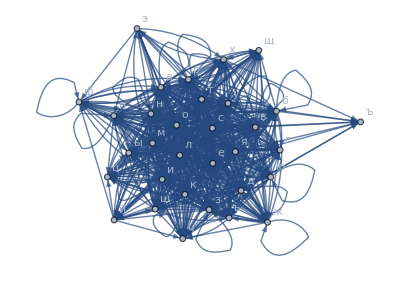

```mathematica
Graph[Keys[rulecounts],EdgeWeight->Values[rulecounts],VertexLabels->All]
```

```mathematica
Graph[)]
```

```mathematica
GraphCenter[%159]
```

{а,г,д,р,ф,б,с,е,з,й,и,л,т,о,к,ю,я,у,ы,в,м,ш,н,х,ь,щ,ж,ц,ч,э,п}

```mathematica
ShowGraph[
```

-Graphics-

```mathematica
BipartiteGraphQ[%155]
```

False

```mathematica
Graph[G]
```

Graph[Graph[{{а,г},{г,а},{а,д},{д,а},{а,р},{р,ф},{б,а},{а,р},{б,а},{а,с},{б,е},{е,г},{б,е},{е,з},{б,е},{е,й},{б,и},{и,л},{б,и},{и,т},{б,о},{о,г},{б,о},{о,й},{б,о},{о,к},{б,о},{о,р},{б,о},{о,ю},225881,{о,в},{в,и},{и,т},{т,е},{е,л},{л,ь},{ь,н},{н,ы},{ы,х},{п,р},{р,е},{е,д},{д,в},{в,о},{о,д},{д,и},{и,т},{т,е},{е,л},{л,ь},{ь,с},{с,т},{т,в},{в,у},{у,е},{е,м},{м,ы},{ы,м},{м,и}}]]
 |  |  |  |

```mathematica
WordList[Language->"Russian"]
```

{ага,ада,арф,бар,бас,бег,без,бей,бил,бит,бог,бой,бок,бор,бою,боя,бук,бык,был,вал,вам,вас,ваш,31756,разглагольствовал,руководствоваться,свидетельствовало,свидетельствующих,сильнодействующие,снисходительности,специализировался,тяжеловооруженных,усовершенствовать,набальзамированных,непредназначенными,неудовлетворенными,полуюмористическое,сверхъестественные,распространявшемуся,сверхъестественному,лесовостановительных,недоброжелательности,председательствовать,предусмотрительность,лесовосстановительных,предводительствуемыми}
 |  |  |  |

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

```mathematica
Graph[{{"a"->"b"},{"b"->"c"}}]
```

Graph[{{a→b},{b→c}}]

```mathematica
First[TextWords/@ToLowerCase/@TextSentences[ExampleData[{"Text","AliceInWonderland"}]]]
```

{i,down,the,rabbit-hole,alice,was,beginning,to,get,very,tired,of,sitting,by,her,sister,on,the,bank,and,of,having,nothing,to,do}

```mathematica
AssociationMap[#[#]&,{1,2,3}]
```

<|1→1[1],2→2[2],3→3[3]|>

```mathematica
N[1[1]]
```

1.[1.]

```mathematica
Interpreter["CurrencyAmount"]["25 russian rubles"]
```

25  ₽

```mathematica
Interpreter["University"]["НГУ" ]
```

Failure[…]

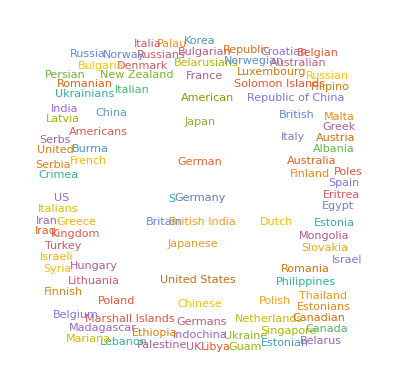

```mathematica
WordCloud[TextCases[WikipediaData["World War 2"],"Country"]]
```

```mathematica
Interpreter["Location"]["Eiffel Tower"]
```

GeoPosition[{48.8583,2.29444}]

```mathematica
Interpreter["University"]["U of T"]
```

University of Toronto

```mathematica
Interpreter["Chemical"][{"C2H4","C2H6","C3H8"}]
```

{ethylene,ethane,propane}

```mathematica
Interpreter["Date"]["20140108"]
```

Day: Wed 8 Jan 2014

```mathematica
Interpreter["University"][#]&/@( StringJoin["U of ",#]&/@(Alphabet[]//ToUpperCase))
```

{Failure[…],University of Birjand,University of California-Berkeley,Failure[…],The University of Edinburgh,Failure[…],University of Georgia,University of Houston,University of Illinois at Urbana-Champaign,Failure[…],Failure[…],University of Lethbridge,University of Michigan-Ann Arbor,Failure[…],Failure[…],University of Phoenix-Online Campus,Failure[…],University of Regina,University of Saskatchewan,University of Toronto,Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…]}

```mathematica
LinguisticAssistant
```

Washington

```mathematica
LinguisticAssistant
```

{Montgomery,Juneau,Phoenix,Little Rock,Sacramento,Denver,Hartford,Dover,Washington,Tallahassee,Atlanta,Honolulu,Boise,Springfield,Indianapolis,Des Moines,Topeka,Frankfort,Baton Rouge,Augusta,Annapolis,Boston,Lansing,Saint Paul,Jackson,Jefferson City,Helena,Lincoln,Carson City,Concord,Trenton,Santa Fe,Albany,Raleigh,Bismarck,Columbus,Oklahoma City,Salem,Harrisburg,Providence,Columbia,Pierre,Nashville,Austin,Salt Lake City,Montpelier,Richmond,Olympia,Charleston,Madison,Cheyenne}

```mathematica
cityList=%
```

{Montgomery,Juneau,Phoenix,Little Rock,Sacramento,Denver,Hartford,Dover,Washington,Tallahassee,Atlanta,Honolulu,Boise,Springfield,Indianapolis,Des Moines,Topeka,Frankfort,Baton Rouge,Augusta,Annapolis,Boston,Lansing,Saint Paul,Jackson,Jefferson City,Helena,Lincoln,Carson City,Concord,Trenton,Santa Fe,Albany,Raleigh,Bismarck,Columbus,Oklahoma City,Salem,Harrisburg,Providence,Columbia,Pierre,Nashville,Austin,Salt Lake City,Montpelier,Richmond,Olympia,Charleston,Madison,Cheyenne}

```mathematica
#["Name"]&/@cityList
```

{Montgomery,Juneau,Phoenix,Little Rock,Sacramento,Denver,Hartford,Dover,Washington,Tallahassee,Atlanta,Honolulu,Boise,Springfield,Indianapolis,Des Moines,Topeka,Frankfort,Baton Rouge,Augusta,Annapolis,Boston,Lansing,Saint Paul,Jackson,Jefferson City,Helena,Lincoln,Carson City,Concord,Trenton,Santa Fe,Albany,Raleigh,Bismarck,Columbus,Oklahoma City,Salem,Harrisburg,Providence,Columbia,Pierre,Nashville,Austin,Salt Lake City,Montpelier,Richmond,Olympia,Charleston,Madison,Cheyenne}

```mathematica
cityNamesList=%
```

{Montgomery,Juneau,Phoenix,Little Rock,Sacramento,Denver,Hartford,Dover,Washington,Tallahassee,Atlanta,Honolulu,Boise,Springfield,Indianapolis,Des Moines,Topeka,Frankfort,Baton Rouge,Augusta,Annapolis,Boston,Lansing,Saint Paul,Jackson,Jefferson City,Helena,Lincoln,Carson City,Concord,Trenton,Santa Fe,Albany,Raleigh,Bismarck,Columbus,Oklahoma City,Salem,Harrisburg,Providence,Columbia,Pierre,Nashville,Austin,Salt Lake City,Montpelier,Richmond,Olympia,Charleston,Madison,Cheyenne}

```mathematica
interpreter= Interpreter["Movie"]
```

Interpreter[Movie]

```mathematica
interpreter[#]&/@cityNamesList
```

{Failure[…],Failure[…],Phoenix,Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Honolulu,Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Annapolis,Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Lincoln,Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Expedition: Bismarck,Columbus,Failure[…],Failure[…],Failure[…],Providence,Failure[…],Failure[…],Nashville,Failure[…],Failure[…],Failure[…],Failure[…],Olympia,Failure[…],Madison,Failure[…]}

```mathematica
movieSrcList=%
```

{Failure[…],Failure[…],Phoenix,Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Honolulu,Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Annapolis,Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Lincoln,Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Expedition: Bismarck,Columbus,Failure[…],Failure[…],Failure[…],Providence,Failure[…],Failure[…],Nashville,Failure[…],Failure[…],Failure[…],Failure[…],Olympia,Failure[…],Madison,Failure[…]}

```mathematica
Head[movieSrcList[[1]]]==Failure
```

True

```mathematica
If[FailureQ[#],Nothing,#]&/@movieSrcList
```

{Phoenix,Honolulu,Annapolis,Lincoln,Expedition: Bismarck,Columbus,Providence,Nashville,Olympia,Madison}

```mathematica
movieSrcList[[1]]==FailureQ
```

Failure[…]==Failure

```mathematica
movieSrcList
```

{Failure[…],Failure[…],Phoenix,Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Honolulu,Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Annapolis,Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Lincoln,Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Expedition: Bismarck,Columbus,Failure[…],Failure[…],Failure[…],Providence,Failure[…],Failure[…],Nashville,Failure[…],Failure[…],Failure[…],Failure[…],Olympia,Failure[…],Madison,Failure[…]}

```mathematica
Interpreter["City"][#]&/@StringJoin/@Permutations[Characters["lima"]]
```

{Lima,Failure[…],Failure[…],Failure[…],Failure[…],Lami,Failure[…],Ilam,Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Milah,Failure[…],Mali,Failure[…],Alim,Failure[…],Failure[…],Failure[…],Amli,Failure[…]}

```mathematica
src=%
```

{Lima,Failure[…],Failure[…],Failure[…],Failure[…],Lami,Failure[…],Ilam,Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Milah,Failure[…],Mali,Failure[…],Alim,Failure[…],Failure[…],Failure[…],Amli,Failure[…]}

```mathematica
src
```

{Lima,Failure[…],Failure[…],Failure[…],Failure[…],Lami,Failure[…],Ilam,Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Milah,Failure[…],Mali,Failure[…],Alim,Failure[…],Failure[…],Failure[…],Amli,Failure[…]}

```mathematica
If[FailureQ[#],Nothing,#]&/@src
```

{Lima,Lami,Ilam,Milah,Mali,Alim,Amli}

```mathematica
TextStructure["What would you rather do: make text structures or draw random trees","ConstituentGraphs"]
```

{-Graphics-}

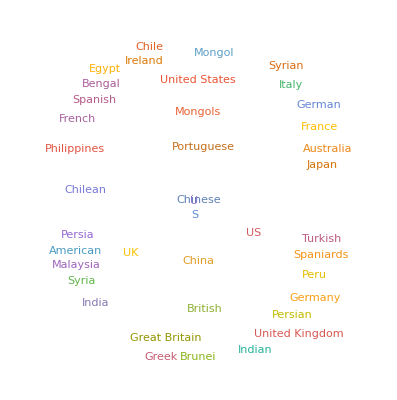

```mathematica
WordCloud[TextCases[WikipediaData["gunpowder"],"Country"]]
```

```mathematica
TextCases["She sells seashells by the sea shore","Noun"]
```

{seashells,sea,shore}

```mathematica
text = WikipediaData["computers"]
```

```mathematica
Length[TextCases[text,#]]&/@{"Noun","Verb","Adjective"}
```

{2451,1507,920}

```mathematica
TextStructure[First[TextSentences[WikipediaData["computers"]]]]
```

A
Determinercomputer
Noun
Noun Phrase  is
Verb    a
Determinermachine
Noun
Noun Phrase    that
Wh-Determiner
Wh-Noun Phrase  can
Verb  be
Verb  programmed
Verb    to
Preposition  carry
Verb  out
Particle
Particle    sequences
Noun
Noun Phrase  of
Preposition  arithmetic
Nounor
Conjunctionlogical
Adjectiveoperations
Noun
Noun Phrase
Prepositional Phrase
Noun Phrase
Verb Phrase
Verb Phrase
Clause  automatically
Adverb
Adverb Phrase
Verb Phrase
Verb Phrase
Verb Phrase
Clause
Noun Phrase
Verb Phrase.
Punctuation
Sentence

```mathematica
(TextCases[ExampleData[{"Text","AliceInWonderland"}],"Noun"]//Counts//Sort)[[-10;;]]
```

<|garden→14,head→16,thing→17,moment→18,way→20,time→21,Mouse→21,voice→22,Rabbit→23,door→23|>

```mathematica
sentence=First[TextSentences[WikipediaData["language"]]]
```

A language is a structured system of communication used by humans, including speech (spoken language), gestures (sign language) and writing.

```mathematica
VertexList[TextStructure[sentence,"ConstituentGraphs"]]
```

```mathematica
CommunityGraphPlot[ TextStructure[sentence,"ConstituentGraphs"][[1]]]
```

-Graphics-

```mathematica
(TextCases[WordList[],#]//Flatten//Length)&/@{"Noun","Verb","Adjective","Adverb"}
```

{22728,5894,7146,2824}

```mathematica
Table[,{j,2,10}]
```

{1,2}

```mathematica
WordTranslation["two","French"]
```

{deux}

```mathematica
WordData
```

```mathematica
CloudDeploy[FormFunction[{"x"->"Integer"},#x!&],"myform"]
```

CloudObject[https://www.wolframcloud.com/obj/eugen.pt/myform]

```mathematica
Clear[f];f[n_]:=Total[Select[Divisors[n],OddQ]]
```

```mathematica
f[1000000]
```

19531